## Signatures of permutations in multiplication table Legendre symbol (Jacoby symbol)

```mathematica
p=17;
(* multiplication table *)
Grid[Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
3 | 6 | 9 | 12 | 15 | 1 | 4 | 7 | 10 | 13 | 16 | 2 | 5 | 8 | 11 | 14
4 | 8 | 12 | 16 | 3 | 7 | 11 | 15 | 2 | 6 | 10 | 14 | 1 | 5 | 9 | 13
5 | 10 | 15 | 3 | 8 | 13 | 1 | 6 | 11 | 16 | 4 | 9 | 14 | 2 | 7 | 12
6 | 12 | 1 | 7 | 13 | 2 | 8 | 14 | 3 | 9 | 15 | 4 | 10 | 16 | 5 | 11
7 | 14 | 4 | 11 | 1 | 8 | 15 | 5 | 12 | 2 | 9 | 16 | 6 | 13 | 3 | 10
8 | 16 | 7 | 15 | 6 | 14 | 5 | 13 | 4 | 12 | 3 | 11 | 2 | 10 | 1 | 9
9 | 1 | 10 | 2 | 11 | 3 | 12 | 4 | 13 | 5 | 14 | 6 | 15 | 7 | 16 | 8
10 | 3 | 13 | 6 | 16 | 9 | 2 | 12 | 5 | 15 | 8 | 1 | 11 | 4 | 14 | 7
11 | 5 | 16 | 10 | 4 | 15 | 9 | 3 | 14 | 8 | 2 | 13 | 7 | 1 | 12 | 6
12 | 7 | 2 | 14 | 9 | 4 | 16 | 11 | 6 | 1 | 13 | 8 | 3 | 15 | 10 | 5
13 | 9 | 5 | 1 | 14 | 10 | 6 | 2 | 15 | 11 | 7 | 3 | 16 | 12 | 8 | 4
14 | 11 | 8 | 5 | 2 | 16 | 13 | 10 | 7 | 4 | 1 | 15 | 12 | 9 | 6 | 3
15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

```mathematica
p=17;
(* powers table *)
Grid[Table[
Mod[j^i,p],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 4 | 9 | 16 | 8 | 2 | 15 | 13 | 13 | 15 | 2 | 8 | 16 | 9 | 4 | 1
1 | 8 | 10 | 13 | 6 | 12 | 3 | 2 | 15 | 14 | 5 | 11 | 4 | 7 | 9 | 16
1 | 16 | 13 | 1 | 13 | 4 | 4 | 16 | 16 | 4 | 4 | 13 | 1 | 13 | 16 | 1
1 | 15 | 5 | 4 | 14 | 7 | 11 | 9 | 8 | 6 | 10 | 3 | 13 | 12 | 2 | 16
1 | 13 | 15 | 16 | 2 | 8 | 9 | 4 | 4 | 9 | 8 | 2 | 16 | 15 | 13 | 1
1 | 9 | 11 | 13 | 10 | 14 | 12 | 15 | 2 | 5 | 3 | 7 | 4 | 6 | 8 | 16
1 | 1 | 16 | 1 | 16 | 16 | 16 | 1 | 1 | 16 | 16 | 16 | 1 | 16 | 1 | 1
1 | 2 | 14 | 4 | 12 | 11 | 10 | 8 | 9 | 7 | 6 | 5 | 13 | 3 | 15 | 16
1 | 4 | 8 | 16 | 9 | 15 | 2 | 13 | 13 | 2 | 15 | 9 | 16 | 8 | 4 | 1
1 | 8 | 7 | 13 | 11 | 5 | 14 | 2 | 15 | 3 | 12 | 6 | 4 | 10 | 9 | 16
1 | 16 | 4 | 1 | 4 | 13 | 13 | 16 | 16 | 13 | 13 | 4 | 1 | 4 | 16 | 1
1 | 15 | 12 | 4 | 3 | 10 | 6 | 9 | 8 | 11 | 7 | 14 | 13 | 5 | 2 | 16
1 | 13 | 2 | 16 | 15 | 9 | 8 | 4 | 4 | 8 | 9 | 15 | 16 | 2 | 13 | 1
1 | 9 | 6 | 13 | 7 | 3 | 5 | 15 | 2 | 12 | 14 | 10 | 4 | 11 | 8 | 16
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

Является ли число x квадратом какого-либо числа y?

Верно ли, что x^((p-1)/2) == 1?

Чётная ли перестановка у строчки x  в таблице умножения?

### Диагональ в таблице умножения

```mathematica
Grid[Table[
If[i==j,Style[Mod[i*j,p],Bold],Mod[i*j,p]],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
3 | 6 | 9 | 12 | 15 | 1 | 4 | 7 | 10 | 13 | 16 | 2 | 5 | 8 | 11 | 14
4 | 8 | 12 | 16 | 3 | 7 | 11 | 15 | 2 | 6 | 10 | 14 | 1 | 5 | 9 | 13
5 | 10 | 15 | 3 | 8 | 13 | 1 | 6 | 11 | 16 | 4 | 9 | 14 | 2 | 7 | 12
6 | 12 | 1 | 7 | 13 | 2 | 8 | 14 | 3 | 9 | 15 | 4 | 10 | 16 | 5 | 11
7 | 14 | 4 | 11 | 1 | 8 | 15 | 5 | 12 | 2 | 9 | 16 | 6 | 13 | 3 | 10
8 | 16 | 7 | 15 | 6 | 14 | 5 | 13 | 4 | 12 | 3 | 11 | 2 | 10 | 1 | 9
9 | 1 | 10 | 2 | 11 | 3 | 12 | 4 | 13 | 5 | 14 | 6 | 15 | 7 | 16 | 8
10 | 3 | 13 | 6 | 16 | 9 | 2 | 12 | 5 | 15 | 8 | 1 | 11 | 4 | 14 | 7
11 | 5 | 16 | 10 | 4 | 15 | 9 | 3 | 14 | 8 | 2 | 13 | 7 | 1 | 12 | 6
12 | 7 | 2 | 14 | 9 | 4 | 16 | 11 | 6 | 1 | 13 | 8 | 3 | 15 | 10 | 5
13 | 9 | 5 | 1 | 14 | 10 | 6 | 2 | 15 | 11 | 7 | 3 | 16 | 12 | 8 | 4
14 | 11 | 8 | 5 | 2 | 16 | 13 | 10 | 7 | 4 | 1 | 15 | 12 | 9 | 6 | 3
15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

```mathematica
Mod[Range[p-1]^2,p]==m
```

{1,4,9,16,8,2,15,13,13,15,2,8,16,9,4,1}==m

```mathematica
Or@@Thread[Mod[Range[(p-1)/2]^2,p]==m]
```

1==m||4==m||9==m||16==m||8==m||2==m||15==m||13==m

```mathematica
LegendreSymbol[m_, p_]:=If[Or@@Thread[Mod[Range[(p-1)/2]^2,p]==m],1,-1];
```

```mathematica
symbols={#, LegendreSymbol[#, p]}&/@Range[p-1];
Grid[symbolsᵀ, Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 1 | -1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | -1 | 1 | 1

### Строчка (p-1) / 2 из таблицы степеней

```mathematica
p=17;
Grid[Table[
If[i==(p-1)/2,Style[Mod[j^i,p],Bold],Mod[j^i,p]],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 4 | 9 | 16 | 8 | 2 | 15 | 13 | 13 | 15 | 2 | 8 | 16 | 9 | 4 | 1
1 | 8 | 10 | 13 | 6 | 12 | 3 | 2 | 15 | 14 | 5 | 11 | 4 | 7 | 9 | 16
1 | 16 | 13 | 1 | 13 | 4 | 4 | 16 | 16 | 4 | 4 | 13 | 1 | 13 | 16 | 1
1 | 15 | 5 | 4 | 14 | 7 | 11 | 9 | 8 | 6 | 10 | 3 | 13 | 12 | 2 | 16
1 | 13 | 15 | 16 | 2 | 8 | 9 | 4 | 4 | 9 | 8 | 2 | 16 | 15 | 13 | 1
1 | 9 | 11 | 13 | 10 | 14 | 12 | 15 | 2 | 5 | 3 | 7 | 4 | 6 | 8 | 16
1 | 1 | 16 | 1 | 16 | 16 | 16 | 1 | 1 | 16 | 16 | 16 | 1 | 16 | 1 | 1
1 | 2 | 14 | 4 | 12 | 11 | 10 | 8 | 9 | 7 | 6 | 5 | 13 | 3 | 15 | 16
1 | 4 | 8 | 16 | 9 | 15 | 2 | 13 | 13 | 2 | 15 | 9 | 16 | 8 | 4 | 1
1 | 8 | 7 | 13 | 11 | 5 | 14 | 2 | 15 | 3 | 12 | 6 | 4 | 10 | 9 | 16
1 | 16 | 4 | 1 | 4 | 13 | 13 | 16 | 16 | 13 | 13 | 4 | 1 | 4 | 16 | 1
1 | 15 | 12 | 4 | 3 | 10 | 6 | 9 | 8 | 11 | 7 | 14 | 13 | 5 | 2 | 16
1 | 13 | 2 | 16 | 15 | 9 | 8 | 4 | 4 | 8 | 9 | 15 | 16 | 2 | 13 | 1
1 | 9 | 6 | 13 | 7 | 3 | 5 | 15 | 2 | 12 | 14 | 10 | 4 | 11 | 8 | 16
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
Mod2[a_,p_]:=Mod[a + (p-1)/2,p]-(p-1)/2;
```

```mathematica
p=17;
Grid[Table[
If[i==(p-1)/2,Style[Mod2[j^i,p],Bold],Mod2[j^i,p]],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | -8 | -7 | -6 | -5 | -4 | -3 | -2 | -1
1 | 4 | -8 | -1 | 8 | 2 | -2 | -4 | -4 | -2 | 2 | 8 | -1 | -8 | 4 | 1
1 | 8 | -7 | -4 | 6 | -5 | 3 | 2 | -2 | -3 | 5 | -6 | 4 | 7 | -8 | -1
1 | -1 | -4 | 1 | -4 | 4 | 4 | -1 | -1 | 4 | 4 | -4 | 1 | -4 | -1 | 1
1 | -2 | 5 | 4 | -3 | 7 | -6 | -8 | 8 | 6 | -7 | 3 | -4 | -5 | 2 | -1
1 | -4 | -2 | -1 | 2 | 8 | -8 | 4 | 4 | -8 | 8 | 2 | -1 | -2 | -4 | 1
1 | -8 | -6 | -4 | -7 | -3 | -5 | -2 | 2 | 5 | 3 | 7 | 4 | 6 | 8 | -1
1 | 1 | -1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | -1 | 1 | 1
1 | 2 | -3 | 4 | -5 | -6 | -7 | 8 | -8 | 7 | 6 | 5 | -4 | 3 | -2 | -1
1 | 4 | 8 | -1 | -8 | -2 | 2 | -4 | -4 | 2 | -2 | -8 | -1 | 8 | 4 | 1
1 | 8 | 7 | -4 | -6 | 5 | -3 | 2 | -2 | 3 | -5 | 6 | 4 | -7 | -8 | -1
1 | -1 | 4 | 1 | 4 | -4 | -4 | -1 | -1 | -4 | -4 | 4 | 1 | 4 | -1 | 1
1 | -2 | -5 | 4 | 3 | -7 | 6 | -8 | 8 | -6 | 7 | -3 | -4 | 5 | 2 | -1
1 | -4 | 2 | -1 | -2 | -8 | 8 | 4 | 4 | 8 | -8 | -2 | -1 | 2 | -4 | 1
1 | -8 | 6 | -4 | 7 | 3 | 5 | -2 | 2 | -5 | -3 | -7 | 4 | -6 | 8 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
PowP2[m_, p_]:= Mod2[ m^((p - 1) / 2) , p];
```

```mathematica
pows={#, PowP2[#, p]}&/@Range[p-1];
Grid[powsᵀ,Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 1 | -1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | -1 | 1 | 1

### Перестановки из таблицы умножения

```mathematica
Grid[Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
], Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
3 | 6 | 9 | 12 | 15 | 1 | 4 | 7 | 10 | 13 | 16 | 2 | 5 | 8 | 11 | 14
4 | 8 | 12 | 16 | 3 | 7 | 11 | 15 | 2 | 6 | 10 | 14 | 1 | 5 | 9 | 13
5 | 10 | 15 | 3 | 8 | 13 | 1 | 6 | 11 | 16 | 4 | 9 | 14 | 2 | 7 | 12
6 | 12 | 1 | 7 | 13 | 2 | 8 | 14 | 3 | 9 | 15 | 4 | 10 | 16 | 5 | 11
7 | 14 | 4 | 11 | 1 | 8 | 15 | 5 | 12 | 2 | 9 | 16 | 6 | 13 | 3 | 10
8 | 16 | 7 | 15 | 6 | 14 | 5 | 13 | 4 | 12 | 3 | 11 | 2 | 10 | 1 | 9
9 | 1 | 10 | 2 | 11 | 3 | 12 | 4 | 13 | 5 | 14 | 6 | 15 | 7 | 16 | 8
10 | 3 | 13 | 6 | 16 | 9 | 2 | 12 | 5 | 15 | 8 | 1 | 11 | 4 | 14 | 7
11 | 5 | 16 | 10 | 4 | 15 | 9 | 3 | 14 | 8 | 2 | 13 | 7 | 1 | 12 | 6
12 | 7 | 2 | 14 | 9 | 4 | 16 | 11 | 6 | 1 | 13 | 8 | 3 | 15 | 10 | 5
13 | 9 | 5 | 1 | 14 | 10 | 6 | 2 | 15 | 11 | 7 | 3 | 16 | 12 | 8 | 4
14 | 11 | 8 | 5 | 2 | 16 | 13 | 10 | 7 | 4 | 1 | 15 | 12 | 9 | 6 | 3
15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

```mathematica
p=17;
sigs={#[[1]],Signature[#]}&/@Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
]
```

{{1,1},{2,1},{3,-1},{4,1},{5,-1},{6,-1},{7,-1},{8,1},{9,1},{10,-1},{11,-1},{12,-1},{13,1},{14,-1},{15,1},{16,1}}

```mathematica
Grid[sigsᵀ, Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 1 | -1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | -1 | 1 | 1

```mathematica
SignP[m_, p_]:=Signature[Table[Mod[m * i,p], {i, 1, p-1}]];
sigs={#,SignP[#, p]}&/@Range[p-1]
```

{{1,1},{2,1},{3,-1},{4,1},{5,-1},{6,-1},{7,-1},{8,1},{9,1},{10,-1},{11,-1},{12,-1},{13,1},{14,-1},{15,1},{16,1}}

```mathematica
sigs==pows
```

True

```mathematica
sigs==symbols
```

True

```mathematica
Теорема: для простых p 
                LegendreSymbol[x, p] == SignP[x, p] == PowP2[x, p]
```

```mathematica
p=17;
{
(LegendreSymbol[#,p]&/@Range[p-1]) == (PowP2[#,p]&/@Range[p-1]),
(SignP[#,p]&/@Range[p-1]) == (PowP2[#,p]&/@Range[p-1]),
(LegendreSymbol[#,p]&/@Range[p-1]) == (SignP[#,p]&/@Range[p-1])
}
```

{True,True,True}

```mathematica
Coprimes[p_]:=Select[Range[p-1], CoprimeQ[#,p]&];
```

```mathematica
Coprimes[12]
```

{1,5,7,11}

```mathematica
PowP2[m_, p_]:= Mod2[ m^(EulerPhi[p]/2) , p]; (* EulerPhi[p] == Length[Coprimes[p]] *)
SignP[m_, p_]:=Signature[Mod[m * #,p]&/@Coprimes[p]];
LegendreSymbol[m_, p_]:=If[Or@@Thread[Mod[Coprimes[p]^2,p]==m],1,-1];
```

```mathematica
p=2 3^3 5 7;
{
(LegendreSymbol[#,p]&/@Coprimes[p]) == (PowP2[#,p]&/@Coprimes[p]),
(SignP[#,p]&/@Coprimes[p]) == (PowP2[#,p]&/@Coprimes[p]),
(LegendreSymbol[#,p]&/@Coprimes[p]) == (SignP[#,p]&/@Coprimes[p])
}
```

{False,True,False}

```mathematica
normals = Select[
Range[400],
(
p=#;
(LegendreSymbol[#,p]&/@Coprimes[p]) == (PowP2[#,p]&/@Coprimes[p])
)&
]
```

{1,2,3,4,5,6,7,9,10,11,13,14,17,18,19,22,23,25,26,27,29,31,34,37,38,41,43,46,47,49,50,53,54,58,59,61,62,67,71,73,74,79,81,82,83,86,89,94,97,98,101,103,106,107,109,113,118,121,122,125,127,131,134,137,139,142,146,149,151,157,158,162,163,166,167,169,173,178,179,181,191,193,194,197,199,202,206,211,214,218,223,226,227,229,233,239,241,242,243,250,251,254,257,262,263,269,271,274,277,278,281,283,289,293,298,302,307,311,313,314,317,326,331,334,337,338,343,346,347,349,353,358,359,361,362,367,373,379,382,383,386,389,394,397,398}

```mathematica
Select[normals,(! PrimePowerQ[#])&]/2
```

{1/2,3,5,7,9,11,13,17,19,23,25,27,29,31,37,41,43,47,49,53,59,61,67,71,73,79,81,83,89,97,101,103,107,109,113,121,125,127,131,137,139,149,151,157,163,167,169,173,179,181,191,193,197,199}

```mathematica
aNumbers = Select[
Range[400],
(
p=#;
(SignP[#,p]&/@Coprimes[p]) == (PowP2[#,p]&/@Coprimes[p])
)&
]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400}

```mathematica
Length[aNumbers]
```

400

```mathematica
FactorInteger[15]
```

{{3,1},{5,1}}

```mathematica
FactorIntegerExpr[n_]:=Wedge@@(Subscript@@@FactorInteger[n]);
SetAttributes[FactorIntegerExpr, Listable];
Clear[Wedge]
```

```mathematica
FactorIntegerExpr[15]
```

3_1⋀5_1

```mathematica
Sort[{Length[#], #}&/@ FactorIntegerExpr[normals]]
```

{{1,Wedge[1_1]},{1,Wedge[2_1]},{1,Wedge[2_2]},{1,Wedge[3_1]},{1,Wedge[3_2]},{1,Wedge[3_3]},{1,Wedge[3_4]},{1,Wedge[3_5]},{1,Wedge[5_1]},{1,Wedge[5_2]},{1,Wedge[5_3]},{1,Wedge[7_1]},{1,Wedge[7_2]},{1,Wedge[7_3]},{1,Wedge[11_1]},{1,Wedge[11_2]},{1,Wedge[13_1]},{1,Wedge[13_2]},{1,Wedge[17_1]},{1,Wedge[17_2]},{1,Wedge[19_1]},{1,Wedge[19_2]},{1,Wedge[23_1]},{1,Wedge[29_1]},{1,Wedge[31_1]},{1,Wedge[37_1]},{1,Wedge[41_1]},{1,Wedge[43_1]},{1,Wedge[47_1]},{1,Wedge[53_1]},{1,Wedge[59_1]},{1,Wedge[61_1]},{1,Wedge[67_1]},{1,Wedge[71_1]},{1,Wedge[73_1]},{1,Wedge[79_1]},{1,Wedge[83_1]},{1,Wedge[89_1]},{1,Wedge[97_1]},{1,Wedge[101_1]},{1,Wedge[103_1]},{1,Wedge[107_1]},{1,Wedge[109_1]},{1,Wedge[113_1]},{1,Wedge[127_1]},{1,Wedge[131_1]},{1,Wedge[137_1]},{1,Wedge[139_1]},{1,Wedge[149_1]},{1,Wedge[151_1]},{1,Wedge[157_1]},{1,Wedge[163_1]},{1,Wedge[167_1]},{1,Wedge[173_1]},{1,Wedge[179_1]},{1,Wedge[181_1]},{1,Wedge[191_1]},{1,Wedge[193_1]},{1,Wedge[197_1]},{1,Wedge[199_1]},{1,Wedge[211_1]},{1,Wedge[223_1]},{1,Wedge[227_1]},{1,Wedge[229_1]},{1,Wedge[233_1]},{1,Wedge[239_1]},{1,Wedge[241_1]},{1,Wedge[251_1]},{1,Wedge[257_1]},{1,Wedge[263_1]},{1,Wedge[269_1]},{1,Wedge[271_1]},{1,Wedge[277_1]},{1,Wedge[281_1]},{1,Wedge[283_1]},{1,Wedge[293_1]},{1,Wedge[307_1]},{1,Wedge[311_1]},{1,Wedge[313_1]},{1,Wedge[317_1]},{1,Wedge[331_1]},{1,Wedge[337_1]},{1,Wedge[347_1]},{1,Wedge[349_1]},{1,Wedge[353_1]},{1,Wedge[359_1]},{1,Wedge[367_1]},{1,Wedge[373_1]},{1,Wedge[379_1]},{1,Wedge[383_1]},{1,Wedge[389_1]},{1,Wedge[397_1]},{2,2_1⋀3_1},{2,2_1⋀3_2},{2,2_1⋀3_3},{2,2_1⋀3_4},{2,2_1⋀5_1},{2,2_1⋀5_2},{2,2_1⋀5_3},{2,2_1⋀7_1},{2,2_1⋀7_2},{2,2_1⋀11_1},{2,2_1⋀11_2},{2,2_1⋀13_1},{2,2_1⋀13_2},{2,2_1⋀17_1},{2,2_1⋀19_1},{2,2_1⋀23_1},{2,2_1⋀29_1},{2,2_1⋀31_1},{2,2_1⋀37_1},{2,2_1⋀41_1},{2,2_1⋀43_1},{2,2_1⋀47_1},{2,2_1⋀53_1},{2,2_1⋀59_1},{2,2_1⋀61_1},{2,2_1⋀67_1},{2,2_1⋀71_1},{2,2_1⋀73_1},{2,2_1⋀79_1},{2,2_1⋀83_1},{2,2_1⋀89_1},{2,2_1⋀97_1},{2,2_1⋀101_1},{2,2_1⋀103_1},{2,2_1⋀107_1},{2,2_1⋀109_1},{2,2_1⋀113_1},{2,2_1⋀127_1},{2,2_1⋀131_1},{2,2_1⋀137_1},{2,2_1⋀139_1},{2,2_1⋀149_1},{2,2_1⋀151_1},{2,2_1⋀157_1},{2,2_1⋀163_1},{2,2_1⋀167_1},{2,2_1⋀173_1},{2,2_1⋀179_1},{2,2_1⋀181_1},{2,2_1⋀191_1},{2,2_1⋀193_1},{2,2_1⋀197_1},{2,2_1⋀199_1}}

```mathematica
Wedge[Subscript[2, 1],y__]:=Wedge[y];
Wedge[Subscript[2, 1]]:=1;
```

```mathematica
Sort[{Length[#], #}&/@ FactorIntegerExpr[normals]]
```

{{0,1},{1,Wedge[1_1]},{1,Wedge[2_2]},{1,Wedge[3_1]},{1,Wedge[3_1]},{1,Wedge[3_2]},{1,Wedge[3_2]},{1,Wedge[3_3]},{1,Wedge[3_3]},{1,Wedge[3_4]},{1,Wedge[3_4]},{1,Wedge[3_5]},{1,Wedge[5_1]},{1,Wedge[5_1]},{1,Wedge[5_2]},{1,Wedge[5_2]},{1,Wedge[5_3]},{1,Wedge[5_3]},{1,Wedge[7_1]},{1,Wedge[7_1]},{1,Wedge[7_2]},{1,Wedge[7_2]},{1,Wedge[7_3]},{1,Wedge[11_1]},{1,Wedge[11_1]},{1,Wedge[11_2]},{1,Wedge[11_2]},{1,Wedge[13_1]},{1,Wedge[13_1]},{1,Wedge[13_2]},{1,Wedge[13_2]},{1,Wedge[17_1]},{1,Wedge[17_1]},{1,Wedge[17_2]},{1,Wedge[19_1]},{1,Wedge[19_1]},{1,Wedge[19_2]},{1,Wedge[23_1]},{1,Wedge[23_1]},{1,Wedge[29_1]},{1,Wedge[29_1]},{1,Wedge[31_1]},{1,Wedge[31_1]},{1,Wedge[37_1]},{1,Wedge[37_1]},{1,Wedge[41_1]},{1,Wedge[41_1]},{1,Wedge[43_1]},{1,Wedge[43_1]},{1,Wedge[47_1]},{1,Wedge[47_1]},{1,Wedge[53_1]},{1,Wedge[53_1]},{1,Wedge[59_1]},{1,Wedge[59_1]},{1,Wedge[61_1]},{1,Wedge[61_1]},{1,Wedge[67_1]},{1,Wedge[67_1]},{1,Wedge[71_1]},{1,Wedge[71_1]},{1,Wedge[73_1]},{1,Wedge[73_1]},{1,Wedge[79_1]},{1,Wedge[79_1]},{1,Wedge[83_1]},{1,Wedge[83_1]},{1,Wedge[89_1]},{1,Wedge[89_1]},{1,Wedge[97_1]},{1,Wedge[97_1]},{1,Wedge[101_1]},{1,Wedge[101_1]},{1,Wedge[103_1]},{1,Wedge[103_1]},{1,Wedge[107_1]},{1,Wedge[107_1]},{1,Wedge[109_1]},{1,Wedge[109_1]},{1,Wedge[113_1]},{1,Wedge[113_1]},{1,Wedge[127_1]},{1,Wedge[127_1]},{1,Wedge[131_1]},{1,Wedge[131_1]},{1,Wedge[137_1]},{1,Wedge[137_1]},{1,Wedge[139_1]},{1,Wedge[139_1]},{1,Wedge[149_1]},{1,Wedge[149_1]},{1,Wedge[151_1]},{1,Wedge[151_1]},{1,Wedge[157_1]},{1,Wedge[157_1]},{1,Wedge[163_1]},{1,Wedge[163_1]},{1,Wedge[167_1]},{1,Wedge[167_1]},{1,Wedge[173_1]},{1,Wedge[173_1]},{1,Wedge[179_1]},{1,Wedge[179_1]},{1,Wedge[181_1]},{1,Wedge[181_1]},{1,Wedge[191_1]},{1,Wedge[191_1]},{1,Wedge[193_1]},{1,Wedge[193_1]},{1,Wedge[197_1]},{1,Wedge[197_1]},{1,Wedge[199_1]},{1,Wedge[199_1]},{1,Wedge[211_1]},{1,Wedge[223_1]},{1,Wedge[227_1]},{1,Wedge[229_1]},{1,Wedge[233_1]},{1,Wedge[239_1]},{1,Wedge[241_1]},{1,Wedge[251_1]},{1,Wedge[257_1]},{1,Wedge[263_1]},{1,Wedge[269_1]},{1,Wedge[271_1]},{1,Wedge[277_1]},{1,Wedge[281_1]},{1,Wedge[283_1]},{1,Wedge[293_1]},{1,Wedge[307_1]},{1,Wedge[311_1]},{1,Wedge[313_1]},{1,Wedge[317_1]},{1,Wedge[331_1]},{1,Wedge[337_1]},{1,Wedge[347_1]},{1,Wedge[349_1]},{1,Wedge[353_1]},{1,Wedge[359_1]},{1,Wedge[367_1]},{1,Wedge[373_1]},{1,Wedge[379_1]},{1,Wedge[383_1]},{1,Wedge[389_1]},{1,Wedge[397_1]}}

```mathematica
NumberFaceB[p_]:=Module[{m,n, pt1,pt2,path},
path=ListPlot[
((
n=#;
m=PolynomialMod[1/n, p];
pt1={Sin[m 2 Pi / p], -Cos[m 2 Pi / p]} ;
pt2={Sin[n 2 Pi / p], -Cos[n 2 Pi / p]};
{pt1,pt1+pt2}
)&/@Coprimes[p]
), 
Joined->True,Axes->False,AspectRatio->Automatic,Mesh->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
];
Show[path, Graphics[Circle[]]]
];
SetAttributes[NumberFaceB, Listable]
```

```mathematica
SetOptions[{ListPlot},GridLines->None];
```

```mathematica
NumberFaceB[normals⟦;;30⟧ ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Доказательства и соотношения

```mathematica
LegendreSymbol[a * b, p] == LegendreSymbol[a, p] LegendreSymbol[b, p];

(a * b)^((p-1)/2) == (a )^((p-1)/2) (b)^((p-1)/2)
```

```mathematica
Mod2[1 a * 2 a * 3 a * 4 a ... (p-1) a, p ]== Mod[1 * 2  * 3  * 4  ... (p-1), p]
Mod[a^(p-1), p] == 1
```

```mathematica
x ==  m^((p - 1) / 2) ;
x^2 == m^(p - 1)= 1;
x == 1 | -1;
```

```mathematica
x^2-1 ==  (x-1) (x+1)
```

```mathematica
Mod[a^2,p]==m;
x^2-m == (x-a) (x+a)
```

0.  x^(p-1)==1 – малая  теорема Ферма;
1. x == a^2, y == b^2, ⇒ x · y == (a·b)^2;
2.  x - a^2==0  имеет два решения, x == a, x == -a; и это разные остатки для p > 2;
3. {1,2, ... ,  p-1} – из половины чисел извлекается корень, а именно из  чисел  1,2,3, ...,((p-1)/2) возведенных в  квадрат.
Если мы будем возводить в квадрать числа ((p-1)/2)+1,  ((p-1)/2)+2, .., то новых значений не получим, так как по модулю p
		это числа -((p-1)/2), ..., -2, -1 (те же самые числа, только с минусом). Значит из второй половины чисел корни не извлекаютсяч;
		
4. Если x == a^2, то x^((p-1)/2) == a^(p-1)==1. То есть верно следствие: LegendreSymbol[x,p] == 1  ⇒  PowP2[x, p] == 1;
5. Пусть m = x^((p-1)/2); тогда  m^2==1 (малая теорема Ферма), то есть m==1 или m==-1 (пункт 2);
6. У уравнения x^((p-1)/2) ==1 есть (p-1)/2 корней: числа x =1, x=2^2, x=3^2, x = ((p-1)/2)^2  подходят, и если мы 
   раскроем (x-1)(x-2^2)(x-3^2)...(x-((p-1)/2)^2 )  и возьмем все коэффициенты по модулю  p, то должно получится  x^((p-1)/2) -1. 
   Остальные числа не могут быть решениями этого уравнения (так как если подставим одно из остальных чисел, то получим произведение (p-1)/2 ненулевых чисел). 
Это  значит (используем 5), что для второй половины остатков x^((p-1)/2) == -1. 
  Ну  или просто замечаем, что из малой теоремы Ферма следует: x^(p-1)-1 ==0,  ⇒ (x^((p-1)/2)-1) (x^((p-1)/2)+1)==0. У каждого из двух множителей по  (p-1)/2 ненулевых корней.
У первого множителя корни – все возможные квадраты. А у второго – все не квадраты. То есть LegendreSymbol == PowP2;

```mathematica
(p | q) * (q | p) = (-1)^((p-1)/2(q-1)/2)
```

## Accumulate

```mathematica
JacobiSymbol[6,2^4]
```

0

```mathematica
JacobiSymbol[-1, #]&/@(2^Range[20])
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

JacobiSymbol[m,2^k*n] == JacobiSymbol[m,n]

```mathematica
l = Accumulate@(JacobiSymbol[11, #]&/@(Range[1000] * 2 + 1));
ListPlot[l]
```

```mathematica
l = Accumulate@(JacobiSymbol[(#-1)/2, #]&/@Prime[Range[2,10000]]);
ListPlot[l]
```

```mathematica
l = Accumulate@(JacobiSymbol[EulerPhi[#], #]&/@Prime[Range[2,10000]]);
ListPlot[l]
```

```mathematica
l = Accumulate@(JacobiSymbol[(#-1)/2, #]&/@(2*Range[3,  1000]+1));
ListPlot[l]
```

```mathematica
ns = (2 * Range[50000] -1 );
l = Accumulate@(JacobiSymbol[#-1, #]&/@ns)  ;
ListPlot[l]
```

```mathematica
({#,JacobiSymbol[-1, #]})&/@(Range[100] 2)
```

{{2,1},{4,1},{6,-1},{8,1},{10,1},{12,-1},{14,-1},{16,1},{18,1},{20,1},{22,-1},{24,-1},{26,1},{28,-1},{30,-1},{32,1},{34,1},{36,1},{38,-1},{40,1},{42,1},{44,-1},{46,-1},{48,-1},{50,1},{52,1},{54,-1},{56,-1},{58,1},{60,-1},{62,-1},{64,1},{66,1},{68,1},{70,-1},{72,1},{74,1},{76,-1},{78,-1},{80,1},{82,1},{84,1},{86,-1},{88,-1},{90,1},{92,-1},{94,-1},{96,-1},{98,1},{100,1},{102,-1},{104,1},{106,1},{108,-1},{110,-1},{112,-1},{114,1},{116,1},{118,-1},{120,-1},{122,1},{124,-1},{126,-1},{128,1},{130,1},{132,1},{134,-1},{136,1},{138,1},{140,-1},{142,-1},{144,1},{146,1},{148,1},{150,-1},{152,-1},{154,1},{156,-1},{158,-1},{160,1},{162,1},{164,1},{166,-1},{168,1},{170,1},{172,-1},{174,-1},{176,-1},{178,1},{180,1},{182,-1},{184,-1},{186,1},{188,-1},{190,-1},{192,-1},{194,1},{196,1},{198,-1},{200,1}}

```mathematica
ns = Select[2 * Range[200], (!PrimePowerQ[#])&]
Mod[Select[ns, JacobiSymbol[-1, #]==-1&]/2,16]
Mod[Select[ns, JacobiSymbol[-1, #]==1&]/2 ,16] (* осстаток 8 – исключение *)
```

{6,10,12,14,18,20,22,24,26,28,30,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292,294,296,298,300,302,304,306,308,310,312,314,316,318,320,322,324,326,328,330,332,334,336,338,340,342,344,346,348,350,352,354,356,358,360,362,364,366,368,370,372,374,376,378,380,382,384,386,388,390,392,394,396,398,400}

{3,6,7,11,12,14,15,3,6,7,8,11,12,14,15,3,6,7,11,12,14,15,0,3,6,7,8,11,12,14,15,3,6,7,11,12,14,15,3,6,7,8,11,12,14,15,0,3,6,7,11,12,14,15,0,3,6,7,8,11,12,14,15,3,6,7,11,12,14,15,3,6,7,8,11,12,14,15,3,6,7,11,12,14,15,0,3,6,7,8,11,12,14,15,0,3,6,7}

{5,9,10,13,1,2,4,5,9,10,13,1,2,4,5,8,9,10,13,1,2,4,5,9,10,13,1,2,4,5,8,9,10,13,0,1,2,4,5,9,10,13,1,2,4,5,8,9,10,13,1,2,4,5,9,10,13,1,2,4,5,8,9,10,13,0,1,2,4,5,9,10,13,0,1,2,4,5,8,9,10,13,1,2,4,5,9,10,13,1,2,4,5,8}

```mathematica
SetOptions[{ListPlot},GridLines->Automatic];
```

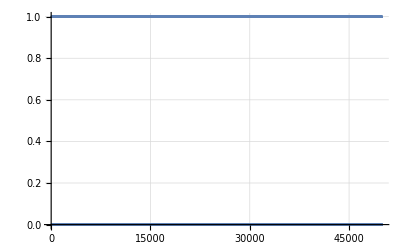

```mathematica
ns = (2 * Range[50000] -1 );
l = Accumulate@(JacobiSymbol[#-1, #]&/@ns)  ;
ListPlot[l]
```

```mathematica
Take[l,100]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}

```mathematica
powers = Select[Range[1000000],PrimePowerQ]; // Timing
```

{7.67592,Null}

```mathematica
powersOdd = Select[powers, OddQ];
```

```mathematica
powersL = Select[Range[50000000],PrimePowerQ];
```

```mathematica
powersLOdd = Select[powersL, OddQ];
```

```mathematica
powersLOdd = Select[Range[50000000],(PrimePowerQ[#] && OddQ[#])&];
```

```mathematica
Length[powersLOdd]
```

3002170

```mathematica
primes = Prime[Range[1000000]];
```

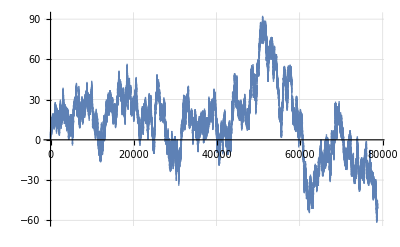

```mathematica
ns =powers;
l = Accumulate@(JacobiSymbol[#-1, #]&/@ns)-Sqrt[ns]/Pi^2 ;
ListPlot[l]
```

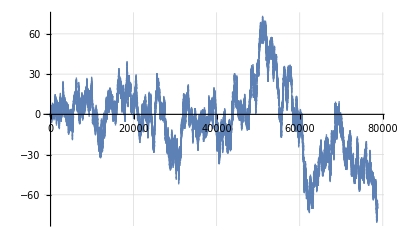

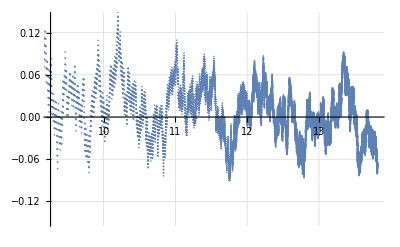

```mathematica
ns =powersOdd;
l = Accumulate@(JacobiSymbol[#-1, #]&/@ns)-Sqrt[ns]/Pi^2 ;
ListPlot[l]

ListPlot[Transpose[{Log[ns], l/Sqrt[ns]}]]
```

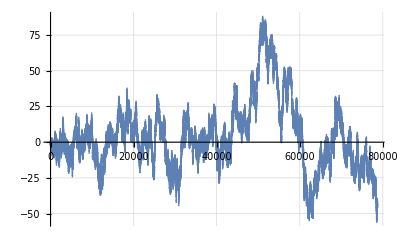

```mathematica
ns =powersOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[#], #]&/@ns)+Sqrt[ns]/Pi^2 ;
ListPlot[l]
```

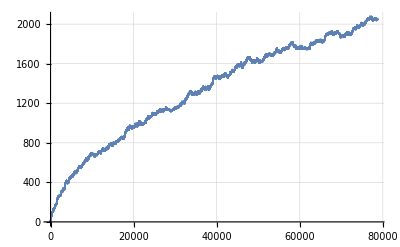

```mathematica
ns =powersOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[EulerPhi[#]], #]&/@ns)-ns/235.0;
ListPlot[l]
```

```mathematica
ns =powersOdd;
y = Accumulate@(JacobiSymbol[EulerPhi[EulerPhi[#]], #]&/@ns);
data = Transpose[{ ns, y}];
```

```mathematica
ans = Fit[data, {1, x, Sqrt[x]}, x ]
```

-23.9383+2.10175 √x+0.00423744 x

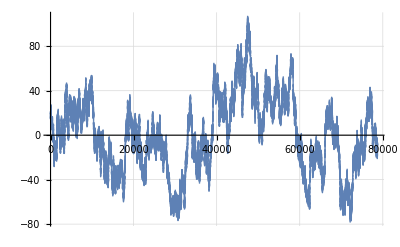

```mathematica
ns =powersOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[EulerPhi[#]], #]&/@ns)-(ans/.{x->ns});
ListPlot[l]
```

```mathematica
ExpSlice[l_, n_]:=Module[
{m, step},
m = Length[l];
step = Log[N[m]]/n;
l⟦ DeleteDuplicates[Round[  Exp[Range[n] * step] ]] ⟧
]
```

```mathematica
ExpSlice[Range[10000], 100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,17,19,21,23,25,28,30,33,36,40,44,48,52,58,63,69,76,83,91,100,110,120,132,145,158,174,191,209,229,251,275,302,331,363,398,437,479,525,575,631,692,759,832,912,1000,1096,1202,1318,1445,1585,1738,1905,2089,2291,2512,2754,3020,3311,3631,3981,4365,4786,5248,5754,6310,6918,7586,8318,9120,10000}

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[-1, #]&/@ns);
xy = N[Transpose[{Log[N[ns]], l/Sqrt[N[ns]]}]];
```

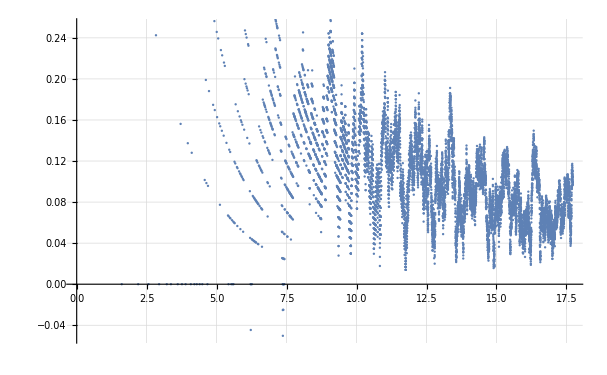

```mathematica
ListPlot[ExpSlice[xy, 20000]]
```

```mathematica
mean = Mean[ N[l]/Sqrt[N[ns]]]
```

0.0759261

```mathematica
1/ mean/Pi
```

4.19236

```mathematica
Ww[x_]:=Exp[-Exp[-x]];
{weights, wsum} =  Plus@@({Ww[#⟦1⟧], Ww[#⟦1⟧] * #⟦2⟧}&/@N[xy]);
weights / wsum / Pi
```

4.19236

```mathematica
mean = Mean[ExpSlice[N[xy⟦1000;;-1⟧], 100000]]⟦2⟧
```

0.0937359

```mathematica
1/mean/Pi
```

3.39581

```mathematica
ns =powersLOdd;
l =N[ Accumulate@(JacobiSymbol[-1, #]&/@ns)];
xy = Transpose[{Log[N[ns]], l/Sqrt[N[ns]]}];
```

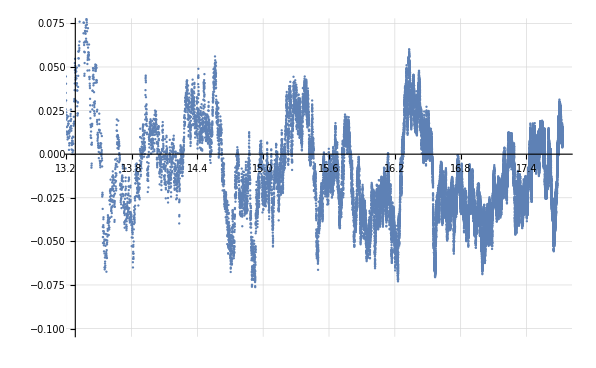

```mathematica
ListPlot[{#[[1]], #[[2]] - 0.09}&/@ xy⟦1;;-1;;53⟧, GridLines->Automatic]
```

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[2, #]&/@ns);
xy = Transpose[{Log[N[ns]], l/Sqrt[N[ns]]}];
```

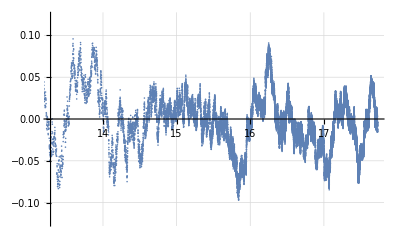

```mathematica
ListPlot[{#⟦1⟧, #⟦2⟧ - 0.09}&/@ xy⟦1;;-1;;53⟧, GridLines->Automatic]
```

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[11, #]&/@ns);
xy = N[Transpose[{Log[ns], l/Sqrt[ns]}]];
```

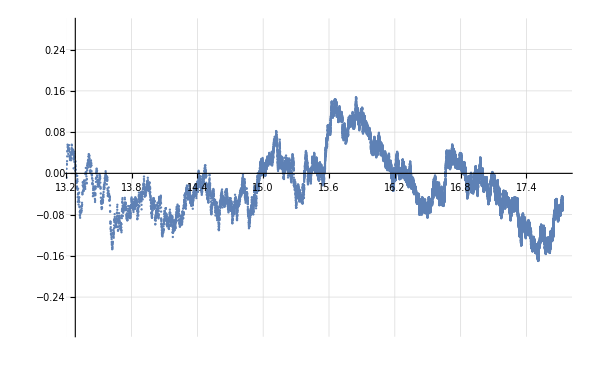

```mathematica
ListPlot[{#⟦1⟧, #⟦2⟧ - 0.09}&/@ xy⟦1;;-1;;53⟧, GridLines->Automatic]
```

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[127, #]&/@ns);
xy = Transpose[{Log[ns], l/Sqrt[ns]}];
```

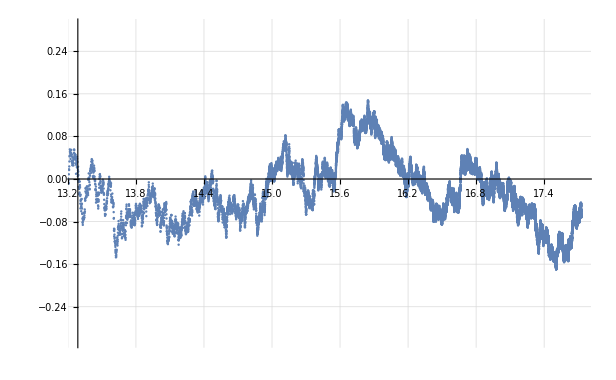

```mathematica
ListPlot[{#⟦1⟧, #⟦2⟧ - 0.09}&/@ xy⟦1;;-1;;53⟧, GridLines->Automatic]
```

```mathematica
ns =primes;
l = N[Accumulate@(JacobiSymbol[-1, #]&/@ns)];
xy = Transpose[{Log[N[ns]], l/Sqrt[N[ns]]}];
```

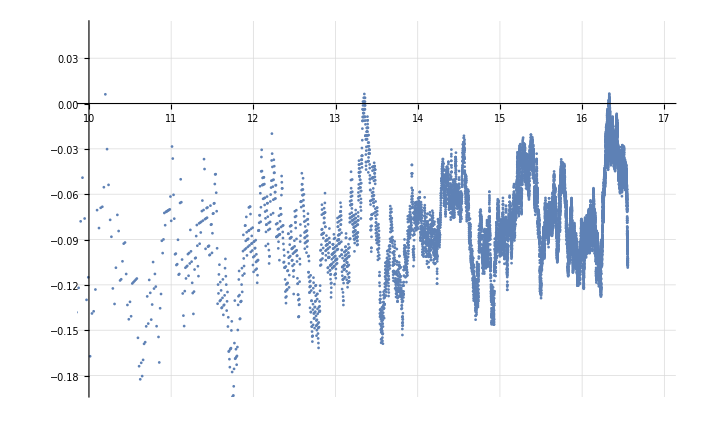

```mathematica
ListPlot[xy⟦1;;-1;;50⟧,PlotRange->{{10,17},Automatic}]
```

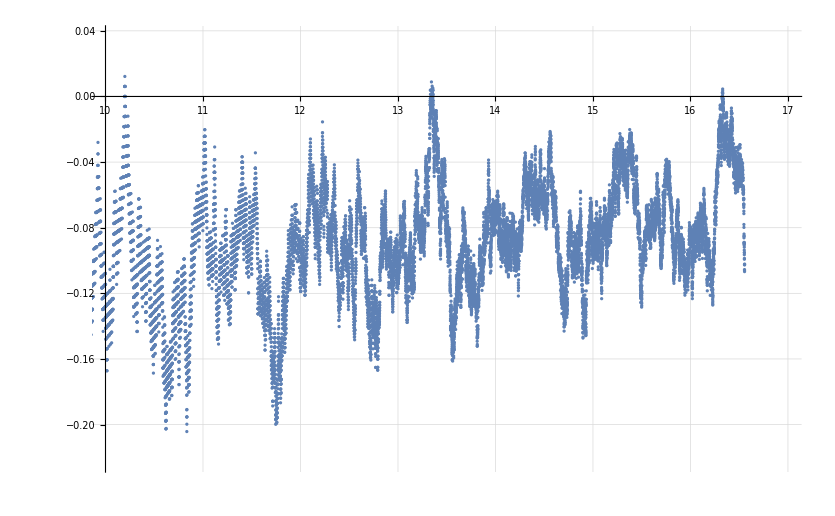

```mathematica
ListPlot[ExpSlice[xy,50000],PlotRange->{{10,17},Automatic}]
```

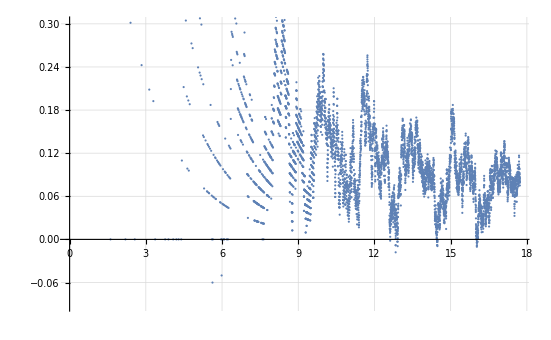

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[#]-1, #]&/@ns);
xy = Transpose[{Log[N[ns]], N[l]/Sqrt[N[ns]]}];
ListPlot[ExpSlice[xy,10000]]
```

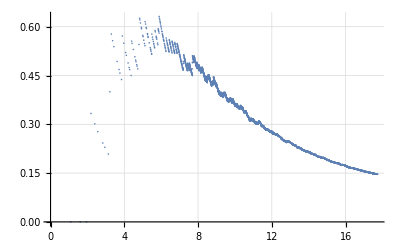

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[#]+1, #]&/@ns);
xy = Transpose[{Log[N[ns]], N[l]/Sqrt[N[ns]]}];
ListPlot[ExpSlice[xy,10000]]
```

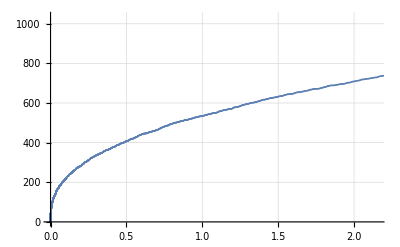

```mathematica
ns =powersLOdd;
l = Accumulate@(JacobiSymbol[EulerPhi[#]+1, #]&/@ns);
xy0 = Transpose[{N[ns], N[l]}];
ListPlot[ExpSlice[xy0,10000]]
```

```mathematica
ans = Fit[xy0, { 1,x^(1/2), x^(1/4), x^(1/8)}, x]
```

-0.612572-7.49143 x^(1/8)+5.37907 x^(1/4)+0.0919531 √x

```mathematica
1/0.0919530962965452
```

10.8751

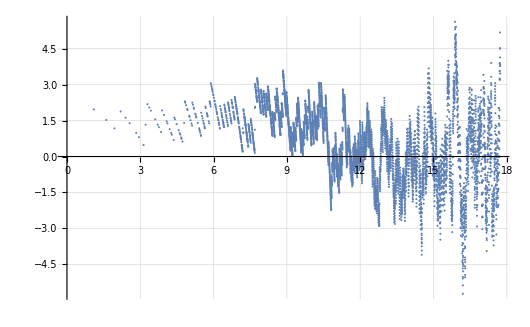

```mathematica
yFit=l  - ((ans)/.{x->ns});
xyFit = Transpose[{Log[N[ns]], yFit }];
ListPlot[ExpSlice[xyFit,10000]]
```

## Coming next

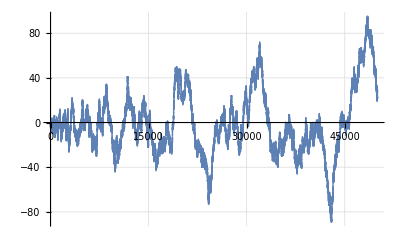

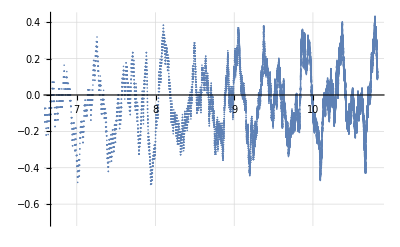

```mathematica
ns = Range[2,50000];
l = N[Accumulate@(MoebiusMu[#]&/@ns)];
ListPlot[l]
ListPlot[Transpose[{Log[ns], l / Sqrt[ns]}]]
```